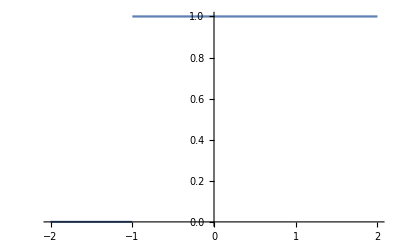

```mathematica
Plot[HeavisideTheta[x+1],{x,-2,2}]
```

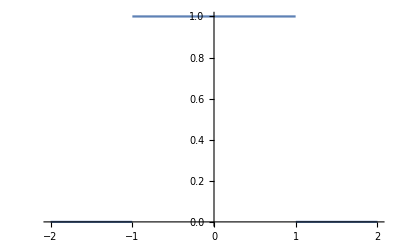

```mathematica
Plot[HeavisideTheta[x+1]-HeavisideTheta[x-1],{x,-2,2}]
```

```mathematica
Plot[HeavisideTheta[x+1]*HeavisideTheta[-x+1],{x,-2,2}]
```

-Graphics-

```mathematica
FourierTransform[HeavisideTheta[x+1]*HeavisideTheta[-x+1],x,k]
```

(√(2/π) Sin[k])/k

```mathematica
FourierTransform[HeavisideTheta[x+1]-HeavisideTheta[x-1],x,k]
```

(√(2/π) Sin[k])/k

```mathematica
Plot3D[HeavisideTheta[1-(x^2+y^2)^(1/2)],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
FourierTransform[HeavisideTheta[1-(x^2+y^2)^(1/2)],{x,y},{kx,ky}]
```

BesselJ[1,√(kx^2+ky^2)]/(√(kx^2+ky^2))

```mathematica
Plot3D[BesselJ[1,√(kx^2+ky^2)]/(√(kx^2+ky^2)),{kx,-10,10},{ky,-10,10}, PlotRange->All]
```

-Graphics3D-